FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

{True,True}

Successfully patched FeynArts.

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe\cede\0.m, 0 diagrams

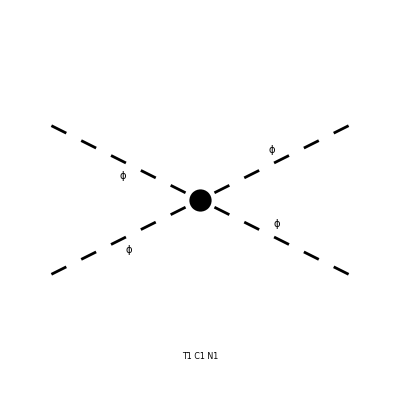

FeynArtsGraphics({ϕ,ϕ}→{ϕ,ϕ})(([T1 C1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

-ⅈ g

g^2

{1/2 (s-2 m^2),1/2 (2 m^2-t)}

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 0 Classes insertions

> Top. 15: 0 Classes insertions

> Top. 16: 1 Classes insertion

> Top. 17: 1 Classes insertion

> Top. 18: 1 Classes insertion

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

> Top. 26: 0 Classes insertions

> Top. 27: 0 Classes insertions

> Top. 28: 0 Classes insertions

> Top. 29: 0 Classes insertions

> Top. 30: 0 Classes insertions

> Top. 31: 0 Classes insertions

> Top. 32: 0 Classes insertions

> Top. 33: 0 Classes insertions

> Top. 34: 0 Classes insertions

> Top. 35: 0 Classes insertions

> Top. 36: 0 Classes insertions

> Top. 37: 0 Classes insertions

> Top. 38: 0 Classes insertions

> Top. 39: 0 Classes insertions

> Top. 40: 0 Classes insertions

> Top. 41: 0 Classes insertions

> Top. 42: 0 Classes insertions

> Top. 43: 0 Classes insertions

> Top. 44: 0 Classes insertions

> Top. 45: 0 Classes insertions

> Top. 46: 0 Classes insertions

> Top. 47: 0 Classes insertions

> Top. 48: 0 Classes insertions

> Top. 49: 0 Classes insertions

> Top. 50: 0 Classes insertions

> Top. 51: 0 Classes insertions

in total: 3 Classes insertions

> Top. 1 aebe\cfdf\efef.m, 0 diagrams

> Top. 2 aebf\cedf\efef.m, 0 diagrams

> Top. 3 aebf\cfde\efef.m, 0 diagrams

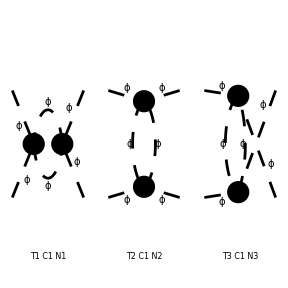

FeynArtsGraphics({ϕ,ϕ}→{ϕ,ϕ})(([T1 C1 N1] | [T2 C1 N2] | [T3 C1 N3]
Null | Null | Null
Null | Null | Null))

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

g^2/(2 (q^2-mphi^2).((-k1-k2+q)^2-mphi^2))+g^2/(2 (q^2-mphi^2).((-k1+p2+q)^2-mphi^2))+g^2/(2 (q^2-mphi^2).((-k2+p2+q)^2-mphi^2))

1/((q^2-m^2).((p1+p2+q)^2-m^2))

1/2 ⅈ π^2 g^2 B_0(s,mphi^2,mphi^2)+1/2 ⅈ π^2 g^2 B_0(t,mphi^2,mphi^2)+1/2 ⅈ π^2 g^2 B_0(u,mphi^2,mphi^2)

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 ac\bc\cc.m, 0 diagrams

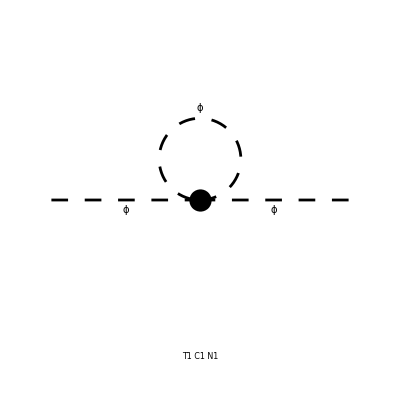

FeynArtsGraphics({ϕ}→{ϕ})(([T1 C1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

1/2 ⅈ π^2 g A_0(mphi^2)

(3 ⅈ g^2)/(32 π^2 eps)+O(eps^0)

(ⅈ g mphi^2)/(32 π^2 eps)+O(eps^0)

```mathematica
(*Simplified phi^4 tutorial:run cells in slide order in one fresh Mathematica kernel.*)(*Requires FeynCalc and its compatible FeynArts add-on.The model directory must contain BOTH Phi4.mod and Phi4.gen.The model-check cell should return {True,True}.Code adapted for teaching;Mathematica was not available to execute it here.*)(* =====Slide 01:01 Load and locate the φ⁴ model=====*)$LoadAddOns={"FeynArts"};
<<FeynCalc`
modelDir=FileNameJoin[{$FeynCalcDirectory,"Examples","Models","Phi4"}];
{FileExistsQ[FileNameJoin[{modelDir,"Phi4.mod"}]],FileExistsQ[FileNameJoin[{modelDir,"Phi4.gen"}]]}
FAPatch[PatchModelsOnly->True,FAModelsDirectory->modelDir];

(* =====Slide 02:02 Draw the tree-level contact=====*)
tree=InsertFields[CreateTopologies[0,2->2],{S[1],S[1]}->{S[1],S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];
Paint[tree]

(* =====Slide 03:03 Calculate the tree amplitude=====*)
faTree=CreateFeynAmp[tree,PreFactor->1];
fcTree=FCFAConvert[faTree,IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},List->False];
fcTree
FullSimplify[Conjugate[-g] (-g),Assumptions->Element[g,Reals]]

(* =====Slide 04:04 Name the scattering channels=====*)
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,m,m,m,m];
{SPD[p1,p2],SPD[p1,k1]}

(* =====Slide 05:05 Draw the one-loop bubbles=====*)
bubbles=InsertFields[CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections}],{S[1],S[1]}->{S[1],S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];
Paint[bubbles]

(* =====Slide 06:06 Convert the bubble amplitude=====*)
faLoop=CreateFeynAmp[bubbles,PreFactor->1];
fcLoop=FCFAConvert[faLoop,IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},ChangeDimension->D,List->False];
fcLoop

(* =====Slide 07:07 Read one bubble denominator=====*)
denS=FAD[{q,m},{q+p1+p2,m}];
denS

(* =====Slide 08:08 Rewrite bubbles as B₀ functions=====*)
bubblePV=ToPaVe[fcLoop/. Mphi->m,q];
bubblePV

(* =====Slide 09:09 Draw the two-point tadpole=====*)
tadpole=InsertFields[CreateTopologies[1,1->1],{S[1]}->{S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]]; 
Paint[tadpole]

(* =====Slide 10:10 Rewrite the tadpole as A₀=====*)
faTad=CreateFeynAmp[tadpole,PreFactor->1];
fcTad=FCFAConvert[faTad,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,List->False];
tadPV=ToPaVe[fcTad/. Mphi->m,q];
tadPV

(* =====Slide 11:11 Find the bubble UV pole=====*)
uvBubble=PaVeUVPart[bubblePV,Prefactor->1/(2 Pi)^D];
Series[uvBubble/. D->4-2 eps,{eps,0,-1}]

(* =====Slide 12:12 Find the tadpole UV pole=====*)
uvTad=PaVeUVPart[tadPV,Prefactor->1/(2 Pi)^D];
Series[uvTad/. D->4-2 eps,{eps,0,-1}]
```